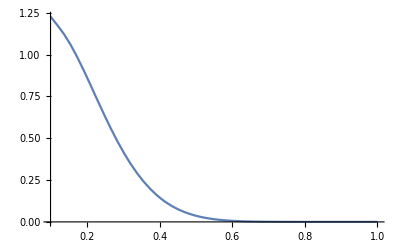

```mathematica
Plot[aHdgf[y,-1],{y,0.1,1}]
```

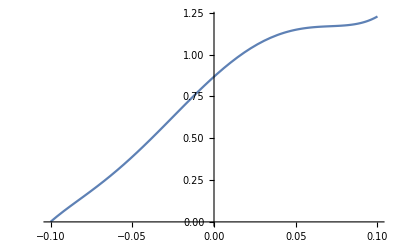

```mathematica
Plot[aHerf[y,-1],{y,-0.1,0.1}]
```

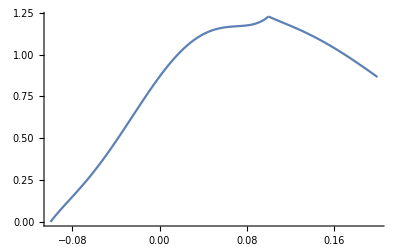

```mathematica
Show[Plot[aHdgf[y,-1],{y,0.1,0.2},PlotRange->All],Plot[aHerf[y,-1],{y,-0.1,0.1},PlotRange->All]]
```

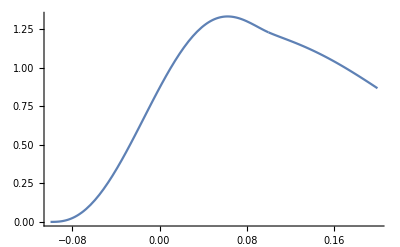

```mathematica
Show[Plot[aHdgf[y,-1],{y,0.1,0.2},PlotRange->All],Plot[aHerf1[y,-1],{y,-0.1,0.1},PlotRange->All]]
```

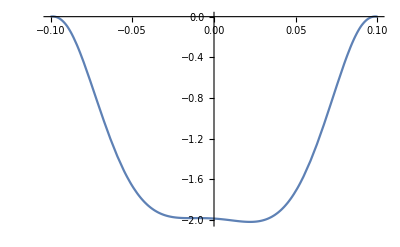

```mathematica
Plot[Re[aHdaf1[y,-1]],{y,-0.1,0.1},PlotRange->All]
```

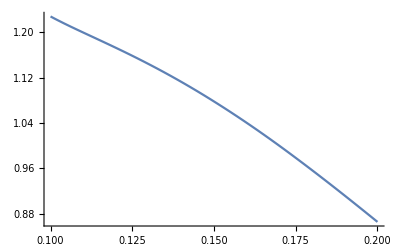

```mathematica
Plot[aHdgf[y,-1],{y,0.1,0.2},PlotRange->All,PlotLegends->"Expressions"]
```

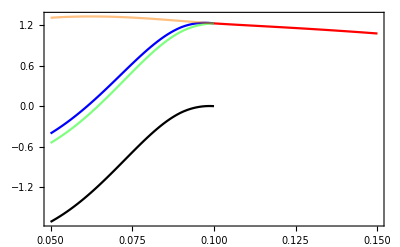
-Graphics-fy

```mathematica
Labeled[Show[Plot[aHdgf[y,-1],{y,0.1,0.15},PlotRange->All,PlotStyle->Red],Plot[Re[aHerf1[y,-1]+aHdaf1[y,-1]],{y,0.05,0.1},PlotRange->All,PlotStyle->Directive[Blue,Opacity[1]]],
Plot[Re[aHerf[y,-1]+aHdaf[y,-1]],{y,0.05,0.1},PlotRange->All,PlotStyle->Directive[Green,Opacity[0.5]]],Plot[Re[aHdaf1[y,-1]],{y,0.05,0.1},PlotRange->All,PlotStyle->Black],Plot[aHerf1[y,-1],{y,0.05,0.1},PlotRange->All,PlotStyle->Directive[Orange,Opacity[0.5]]],Frame->True,FrameStyle->Directive[Thick,20]],{f,y},{Left,Bottom}]
```

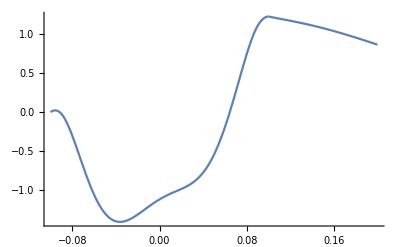

```mathematica
Show[Plot[aHdgf[y,-1],{y,0.1,0.2},PlotRange->All],Plot[Re[aHerf[y,-1]+aHdaf[y,-1]],{y,-0.1,0.1},PlotRange->All]]
```

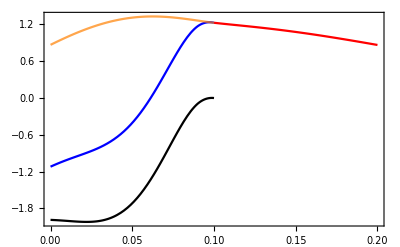
-Graphics-H_ux

```mathematica
hnd=Labeled[Show[Plot[aHdgf[y,-1],{y,0.1,0.2},PlotRange->All,PlotStyle->Red],Plot[Re[aHdaf1[y,-1]],{y,0,0.1},PlotRange->All,PlotStyle->Black],Plot[aHerf1[y,-1]+Re[aHdaf1[y,-1]],{y,0,0.1},PlotRange->All,PlotStyle->Directive[Blue,Opacity[1]]],
Plot[aHerf1[y,-1],{y,0,0.1},PlotRange->All,PlotStyle->Directive[Orange,Opacity[0.7]]],Frame->True,FrameStyle->Directive[Thick,20]],{"H_u","x"},{Left,Bottom}]
```

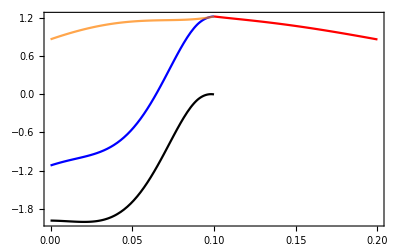
-Graphics-H_ux

```mathematica
hd=Labeled[Show[Plot[aHdgf[y,-1],{y,0.1,0.2},PlotRange->All,PlotStyle->Red],Plot[Re[aHdaf[y,-1]],{y,0,0.1},PlotRange->All,PlotStyle->Black],Plot[aHerf[y,-1]+Re[aHdaf[y,-1]],{y,0,0.1},PlotRange->All,PlotStyle->Directive[Blue,Opacity[1]]],
Plot[aHerf[y,-1],{y,0,0.1},PlotRange->All,PlotStyle->Directive[Orange,Opacity[0.7]]],Frame->True,FrameStyle->Directive[Thick,20]],{"H_u","x"},{Left,Bottom}]
```

```mathematica
hd2=Labeled[Show[Plot[aHdgf[y,-1],{y,0.1,0.2},PlotRange->All,PlotStyle->Red],Plot[Re[aHdaf[y,-1]],{y,0,0.1},PlotRange->All,PlotStyle->Black],Plot[aHerf[y,-1]+Re[aHdaf[y,-1]],{y,0,0.1},PlotRange->All,PlotStyle->Directive[Blue,Opacity[1]]],
Plot[aHerf[y,-1],{y,0,0.1},PlotRange->All,PlotStyle->Directive[Orange,Opacity[0.7]]],Frame->True,FrameStyle->Directive[Thick,20]],{"H_u","x"},{Left,Bottom}]
```

-Graphics-H_ux

```mathematica
pathh2dnD=FileNameJoin[{"G:\\calc-online\\gpd\\juanjiclac\\juanji\\Dtermtest\\re",
"h-a-2d-noD.pdf"}];
Export[pathh2dnD,hnd]
pathh2dD=FileNameJoin[{"G:\\calc-online\\gpd\\juanjiclac\\juanji\\Dtermtest\\re",
"h-a-2d-D.pdf"}];
Export[pathh2dD,hd]
```

G:\calc-online\gpd\juanjiclac\juanji\Dtermtest\re\h-a-2d-noD.pdf

G:\calc-online\gpd\juanjiclac\juanji\Dtermtest\re\h-a-2d-D.pdf